Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

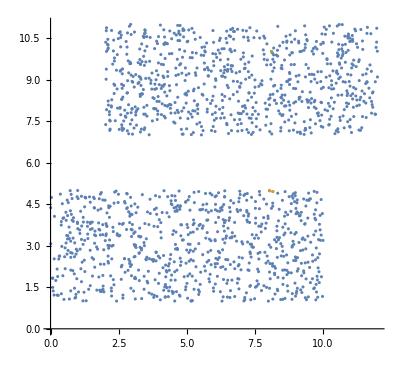

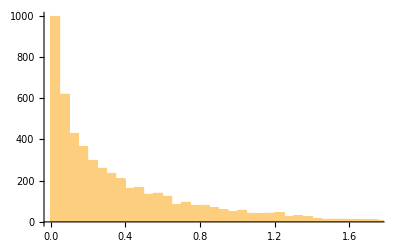

Nejbližší vysílač je na konvexní obálce v 4885 z 10000 případů.

Průměrná vzdálenost Transmitter -> Sink: 4.11199

Průměrná vzdálenost TransmitterOnCH -> Sink: 4.30096

Průměrná vzdálenost vysílačů pouze na konv. ob.: 1.24997

Průměrná vzdálenost vysílačů jeden mimo konv. ob.: 0.159537

Průměrná vzdálenost vysílačů při hledání ze všech (pokud byl první nalezený bod blíže než na konvexní obálce): 0.155108

Při hledání druhého vysílače mimo konvexní obálku jsme dosáhli menší vzdálenosti v 9208 z 10000 případů.

```mathematica
(*Global Variables*)
numOfPoints = 800;
numOfTests = 10000;

(*Distributin function for generating point on given region*)
RegionDistribution/:
Random`DistributionVector[RegionDistribution[reg_MeshRegion],n_Integer,prec_?Positive]:=Module[{d=RegionDimension@reg,cells,measures,s,m},cells=Developer`ToPackedArray@MeshPrimitives[reg,d][[All,1]];
s=RandomVariate[DirichletDistribution@ConstantArray[1,d+1],n];
measures=PropertyValue[{reg,d},MeshCellMeasure];
m=RandomVariate[#,n]&@EmpiricalDistribution[measures->Range@Length@cells];
#[[All,1]] (1-Total[s,{2}])+Total[#[[All,2;;]] s,{2}]&@cells[[m]]]

(*(*Initialize of two CIRCLE regions*)
region1 = DiscretizeRegion@Disk[{10,10}, 10];
region2 = DiscretizeRegion@Disk[{30,30}, 10];*)

(*(*Initialize of two POLYGON regions*)
region1 = DiscretizeRegion@Polygon[{{2,1},{3,1},{4,2},{4,3},{3.75, 3.75}, {3, 4}, {2, 4}, {1, 3}, {1, 2}}];
region2 = DiscretizeRegion@Polygon[{{5,2}, {7,2}, {7,7}, {2,7}, {2, 5}, {4, 5}, {5, 4}}];*)

true = 0;
closer = 0;
closest = 0.0;
distTransmittersBothOnCH = 0.0;
distTransmittersOneOnCH = 0.0;
distTransmitters = 0.0;

distTransmitterSink = 0.0;
distTransmitterOnCHSink = 0.0;

distList={};
sink;

Do[
Module[{},

(*Initialize of two RECTANGLE regions*)
region1 = DiscretizeRegion@Rectangle[{0,1},{10,5}];
region2 = DiscretizeRegion@Rectangle[{2,7},{12,11}];

pts1= RandomVariate[RegionDistribution[region1],numOfPoints];
pts2= RandomVariate[RegionDistribution[region2],numOfPoints];
sink = RandomSample[pts2, 1];
area = Join[pts1, pts2];

(*Exctract points on convex hull - both regions*)
convexHullpts1 = RegionBoundary[ConvexHullMesh[pts1]];
convexHullpts2 = RegionBoundary[ConvexHullMesh[pts2]];

arrayOneConvexHull = pts1;
cutConvexHull1[x_]=If[RegionMember[convexHullpts1,arrayOneConvexHull[[x]]],(*Print[arrayOneConvexHull[[x]]]*), arrayOneConvexHull = Delete[arrayOneConvexHull, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull1[i]];

transmitterOnCH = Flatten[Nearest[arrayOneConvexHull, sink],1];
transmittersBothOnCH = Flatten[Nearest[arrayOneConvexHull,transmitterOnCH,{2,5}],1];
transmittersOneOnCH =  Flatten[Nearest[pts1,transmitterOnCH,{2,5}],1];
transmitter = Flatten[Nearest[pts1, sink],1];

r = EuclideanDistance[transmitterOnCH,sink];
distTransmitterOnCHSink += r;
s = EuclideanDistance[transmitter,sink];
distTransmitterSink += s;

a= EuclideanDistance[transmittersBothOnCH[[1]],transmittersBothOnCH[[2]]];
b= EuclideanDistance[transmittersOneOnCH[[1]],transmittersOneOnCH[[2]]];
distTransmittersBothOnCH +=a;
distTransmittersOneOnCH += b;
If[(a > b),closer++];

If[(transmitter == transmitterOnCH), 
true++;,
transmitters = Flatten[Nearest[pts1,transmitter,{2,5}],1];
c = EuclideanDistance[transmitters[[1]],transmitters[[2]]];
distTransmitters += c;
closest++;
t = r - s;
distList = Append[distList, t];
]


],{numOfTests}]

ListPlot[{area, transmittersOneOnCH, sink}, AspectRatio->Automatic]
Histogram[distList]

distTransmittersBothOnCH = distTransmittersBothOnCH/numOfTests;
distTransmittersOneOnCH = distTransmittersOneOnCH/numOfTests;
distTransmitters = distTransmitters/closest;
distTransmitterSink = distTransmitterSink/numOfTests;
distTransmitterOnCHSink = distTransmitterOnCHSink/numOfTests;

Print["Nejbližší vysílač je na konvexní obálce v ", true , " z ", numOfTests ," případů. "]
Print[""]
Print["Průměrná vzdálenost Transmitter -> Sink: ", distTransmitterSink]
Print["Průměrná vzdálenost TransmitterOnCH -> Sink: ", distTransmitterOnCHSink ]
Print[""]
Print["Průměrná vzdálenost vysílačů pouze na konv. ob.: ",distTransmittersBothOnCH]
Print["Průměrná vzdálenost vysílačů jeden mimo konv. ob.: ",distTransmittersOneOnCH]
Print["Průměrná vzdálenost vysílačů při hledání ze všech (pokud byl první nalezený bod blíže než na konvexní obálce): ",distTransmitters]

Print["Při hledání druhého vysílače mimo konvexní obálku jsme dosáhli menší vzdálenosti v ", closer , " z ",numOfTests ," případů. "]
(*Print["Při hledání ze všech bodů byly nalezné body nejblíže sobě v  ", closest , " z ",numOfTests ," případů. "]*)
```